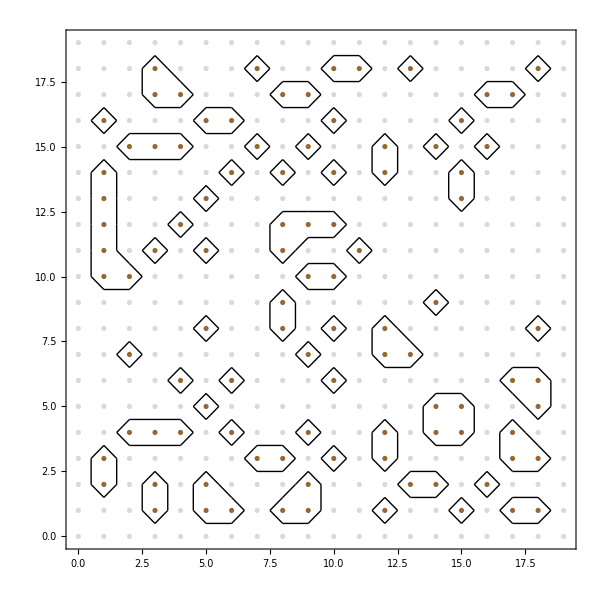

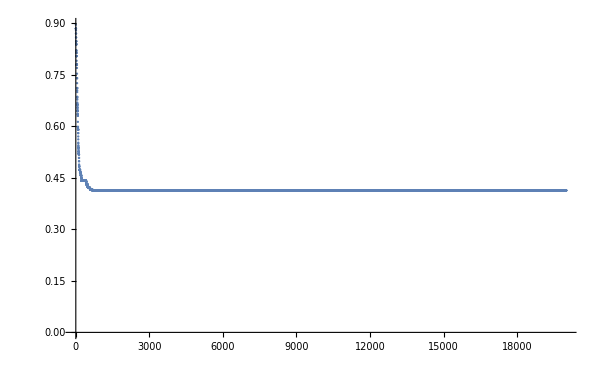

```mathematica
infoData=Import[NotebookDirectory[]<>"out/x64-Release/output-info.txt","Table"];

data=Import[NotebookDirectory[]<>"out/x64-Release/output-boundary.txt","Table"];
data=Partition[#,2]&/@data;

rawdata=Import[NotebookDirectory[]<>"out/x64-Release/output-raw.txt","Table"];
disks=MapIndexed[{If[#1==1,Brown,LightGray],Disk[#2-{1,1},0.1]}&,Transpose@rawdata,{2}];

Graphics[{disks,Line[data]},ImageSize->600,Frame->True]

ListPlot[infoData,PlotRange->All]
```

```mathematica
LoadCube[filename_]:=Module[{d,dims,dataAndHeaders, file = OpenRead[filename, BinaryFormat->True]},
d=First@BinaryReadList[file, "Integer32",1];
dims=BinaryReadList[file, "Integer32",d];
Print["Dimensions: ",dims];
dataAndHeaders=TakeDrop[BinaryReadList[file, "Real64"],Times@@dims];
Close[file];
{ArrayReshape[dataAndHeaders[[1]],dims],TakeList[dataAndHeaders[[2]],dims]}]
```

```mathematica
{partics, headers}=LoadCube[NotebookDirectory[]<>"out/x64-Release/glass2d.binary"];
Manipulate[ListPlot[partics[[i,All,{1,2}]], PlotRange->{{0,1},{0,1}},PlotStyle->PointSize[0.01],Frame->True,AspectRatio->1,ImageSize->600],{i,1,Length@partics,1}]
```

Dimensions: {501,500,9}

```mathematica
(*Indices are: x,y, velX,velY, dens, press, intEnergy, kinEnergy, Dummy*)
```

```mathematica
Manipulate[ListDensityPlot[{#[[1]],#[[2]],#[[5]]}&/@partics[[i]], PlotRange->{{0,1},{0,1},All},
Mesh->All,InterpolationOrder->0,ColorFunction->ColorData[{"Rainbow",{0.5,1.2}}],ColorFunctionScaling->False,ClippingStyle->Automatic,
PlotLegends->Automatic,Frame->True,AspectRatio->1,ImageSize->600],{i,1,Length@partics,1}]
```